## Variance-stabilizing transformation for DESeq

```mathematica
For parametrized dispersion fit
```

This file describes the variance stabilizing transformation (VST) used by DESeq when parametric dispersion estimation is used.
This is a Mathematica notebook. The file vst.pdf is produced from vst.nb.

When using estimateDispersions with fitType="parametric", we parametrize the relation between mean μ and dispersion α with two constants a_0 and a_1as follows:

```mathematica
α = Subscript[a, 0]+Subscript[a, 1]/μ
```

a_0+a_1/μ

In the package, a_0 is called the asymptotic dispersion and a_1 the extra-Poisson factor.

The variance is hence

```mathematica
v = μ + α μ^2//Expand
```

μ+μ^2 a_0+μ a_1

A variance stabilizing transformation (VST) is a transformation u, such that, if X is a random variable with variance-mean relation v, i.e.,Var(X)=v(E(X)), then u(X) has stabilized variance, i.e., is homoskedastic.

A VST u can be derived from a variance-mean relation v by u(x) =∫^x dμ/(√(v(μ))). 
Hence, we can get a general VST with

```mathematica
Subscript[u, 0]=Integrate[ 1/(√v),{μ,0,x}, Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

Log[(1+2 x a_0+a_1+2 √(x a_0 (1+x a_0+a_1)))/(1+a_1)]/(√a_0)

If u_0 is a VST, then so is u(x)=η u_0(x)+ξ. Hence, this here is a VST, too:

```mathematica
u = η Subscript[u, 0] + ξ
```

ξ+(η Log[(1+2 x a_0+a_1+2 √(x a_0 (1+x a_0+a_1)))/(1+a_1)])/(√a_0)

We will now choose the parameters η and ξ such that our VST behaves like log_2 for large values. Let us first look at the asymptotic ratio of the two transformations:

```mathematica
Limit[u/Log[2,x],x->∞,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

(η Log[2])/(√a_0)

Hence, if we set η as follows, both tranformations have asymptotically the ratio 1.

```mathematica
η=(√Subscript[a, 0])/Log[2]
```

(√a_0)/Log[2]

We also want the difference to vanish for large values:

```mathematica
Limit[u-Log[2,x],x->∞,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

ξ+Log[(4 a_0)/(1+a_1)]/Log[2]

So, we set

```mathematica
ξ=-Log[(4 Subscript[a, 0])/(1+Subscript[a, 1])]/Log[2]
```

-Log[(4 a_0)/(1+a_1)]/Log[2]

Check that both limits are now correct:

```mathematica
Limit[u/Log[2,x],x->∞,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

1

```mathematica
Limit[u-Log[2,x],x->∞,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

0

Hence, we arrive at this VST:

```mathematica
FullSimplify[u,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]
```

Log[(1+2 x a_0+a_1+2 √(x a_0 (1+x a_0+a_1)))/(4 a_0)]/Log[2]

This VST (red) now behaves asymptotically as log_2 (blue), shown here for typical values for a_0 and a_1.

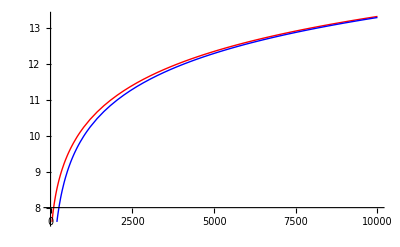

```mathematica
Plot[ {u/.{Subscript[a, 0]->.01,Subscript[a, 1]->3},Log[2,x]},{x,0,10000},PlotStyle->{Red,Blue}]
```

For small values, however, the VST (red) compresses the dynamics much more dramatically than the logarithm (blue) and the identity (green). This reflects that the strong Poisson noise makes differences uninformative for small values.

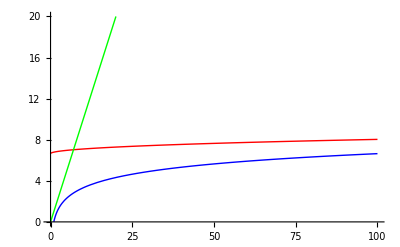

```mathematica
Plot[ {u/.{Subscript[a, 0]->.01,Subscript[a, 1]->3},Log[2,x], x},{x,0,100},PlotStyle->{Red,Blue,Green},PlotRange->{0,20}]
```

A template for the R code in the function:

```mathematica
CForm[FullSimplify[u,Assumptions->{Subscript[a, 0]>0,Subscript[a, 1]>0,x>0}]]/.{Subscript[a, 0]->asymptDisp,Subscript[a, 1]->extraPois,x->q}
```

Log((1 + extraPois + 2*asymptDisp*q + 
       2*Sqrt(asymptDisp*q*(1 + extraPois + asymptDisp*q)))/
     (4.*asymptDisp))/Log(2)

```mathematica
For local dispersion fit
```

In case of a local dispersion fit, the variance-stabilizing transformation u(x) =∫^x dμ/(√(v(μ)))is obtained by numerical integration of the fitted mean-dispersion relation v(μ) (by adding up along a asinh-spaced grid and a fitting a spline). Then, the scaling parameters η and ξ (see above) are chosen such that the VST is equal to log_2 for two large normalized count values (for which the 95- and the 99.9-percentile of the sample-averaged normalized count values are used.)